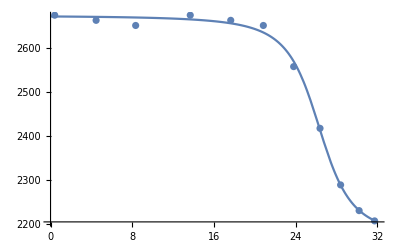

{nu0→2421.58,h→117.247,v→34.3522,t0→26.2734}

h = 117.247 m

v = 123.668 kmph

l = 1.34554m

```mathematica
Clear["Global`*"];
Coords={{645.189664650907,120.131940626718},{618.6695986805937,120.92358438702587},{587.0038482682793,122.90269378779553},{551.7757009345794,127.25673446948875},{506.65200659703135,132.00659703133593},{454.7993402968664,135.17317207256738},{398.98845519516215,135.56899395272129},{329.7196261682243,135.96481583287522},{236.30566245189667,135.17317207256738},{168.62012094557448,135.56899395272129},{97.7680043980209,135.96481583287522}};
Maxima={{545.0467289719626,95.98680593732826},{544.6509070918087,88.07036833424962},{545.0467289719626,79.75810885101708},{545.0467289719626,71.05002748763059}};
BenchmarkVals={{30,8000},{0,0}};
BenchmarkCoords={{615.1072017592084,316.4595931830676},{90.64321055525014,45.32160527762511}};
sol=Solve[{{ax,ay}BenchmarkCoords⟦1⟧+{bx,by}==BenchmarkVals⟦1⟧,{ax,ay}BenchmarkCoords⟦2⟧+{bx,by}==BenchmarkVals⟦2⟧},{ax,ay,bx,by}]⟦1⟧;
transform[c_]:=({ax,ay}/.sol)c+({bx,by}/.sol);
cs=330;
funcFit[{nu0_,h_,v_,t0_},t_]:=nu0(1-((v/cs)^2(t-t0)/(h/cs))/(√(1+((v/cs)(t-t0)/(h/cs))^2)));
variables={nu0,h,v,t0};
model=funcFit[variables,t];
fit=FindFit[transform/@Coords,model,{{nu0,2000},h,v,{t0,25}},t];
Show[
Plot[funcFit[variables/.fit,t],{t,0,32}],
ListPlot[transform/@Coords,PlotRange->{{0,32},{1500,3000}}]
]
Print[fit]
Print["h = ",h/.fit," m"]
Print["v = ",(v/.fit)3.6," kmph"]
Print["l = ",cs/Mean[-Differences[(transform/@Maxima)[[All,2]]]],"m"]
```

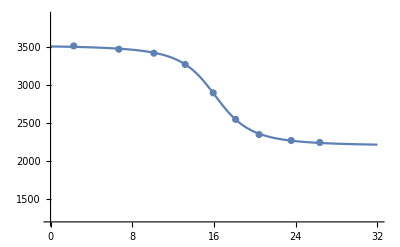

{nu0→2860.47,h→284.175,v→76.436,t0→16.1072}

h = 284.175 m

v = 275.17 kmph

l = 0.811765m

```mathematica
Clear["Global`*"];
Coords={{385.46052631578954,120.88547191731797},{354.0789473684211,121.77362981205482},{318.84868421052636,124.43810349626534},{293.0921052631579,131.24731402258112},{268.5197368421053,143.089419285739},{237.7302631578948,155.81968244363375},{203.38815789473688,160.85257718047586},{164.9013157894737,162.62889296994956},{115.4605263157895,164.1091561278443}};
Maxima={{262.59868421052636,109.16768563031138},{262.8947368421053,93.1808435250482},{264.37500000000006,77.49005405136398},{264.9671052631579,65.0558435250482},{265.55921052631584,53.8058435250482}};
BenchmarkVals={{30,8000},{0,0}};
BenchmarkCoords={{426.3157894736843,316.8723140225811},{90.00000000000001,44.50389296994956}};
sol=Solve[{{ax,ay}BenchmarkCoords⟦1⟧+{bx,by}==BenchmarkVals⟦1⟧,{ax,ay}BenchmarkCoords⟦2⟧+{bx,by}==BenchmarkVals⟦2⟧},{ax,ay,bx,by}]⟦1⟧;
transform[c_]:=({ax,ay}/.sol)c+({bx,by}/.sol);
cs=330;
funcFit[{nu0_,h_,v_,t0_},t_]:=nu0(1-((v/cs)^2(t-t0)/(h/cs))/(√(1+((v/cs)(t-t0)/(h/cs))^2)));
variables={nu0,h,v,t0};
model=funcFit[variables,t];
fit=FindFit[transform/@Coords,model,{{nu0,3000},h,v,{t0,18}},t];
Show[
Plot[funcFit[variables/.fit,t],{t,0,32},PlotRange->{{0,32},{1200,3900}}],
ListPlot[transform/@Coords]
]
Print[fit]
Print["h = ",h/.fit," m"]
Print["v = ",(v/.fit)3.6," kmph"]
Print["l = ",cs/Mean[-Differences[(transform/@Maxima)[[All,2]]]],"m"]
```

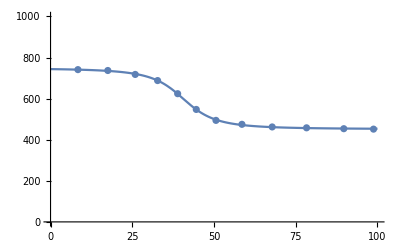

{nu0→599.853,h→866.196,v→81.8027,t0→40.5561}

h = 866.196 m

v = 294.49 kmph

l = 2.42086m

```mathematica
Clear["Global`*"];
Coords={{611.6097952629466,105.91950206197771},{563.6290646326777,106.20854260794317},{503.50863107185876,106.7866236998741},{448.01284624648736,107.36470479180508},{399.16499397832195,109.09894806759792},{357.254114813328,111.7003129812872},{325.4596547571257,118.92632663042411},{295.3994379767162,129.33178628518124},{263.02689682858295,138.0030026641455},{226.89682858289845,142.04957030766218},{182.67362505018068,144.65093522135146},{134.40385387394622,145.2290163132824}};
Maxima={{315.6322761942995,101.88521299634141},{316.2103572862304,82.51949641665453},{315.34323564833403,64.8880231127605}};
BenchmarkVals={{100,2000},{0,0}};
BenchmarkCoords={{617.9686872741871,316.0519789788786},{90.18065034122844,44.64290631729688}};
sol=Solve[{{ax,ay}BenchmarkCoords⟦1⟧+{bx,by}==BenchmarkVals⟦1⟧,{ax,ay}BenchmarkCoords⟦2⟧+{bx,by}==BenchmarkVals⟦2⟧},{ax,ay,bx,by}]⟦1⟧;
transform[c_]:=({ax,ay}/.sol)c+({bx,by}/.sol);
cs=330;
funcFit[{nu0_,h_,v_,t0_},t_]:=nu0(1-((v/cs)^2(t-t0)/(h/cs))/(√(1+((v/cs)(t-t0)/(h/cs))^2)));
variables={nu0,h,v,t0};
model=funcFit[variables,t];
fit=FindFit[transform/@Coords,model,{{nu0,500},h,v,{t0,40}},t];
Show[
Plot[funcFit[variables/.fit,t],{t,0,100},PlotRange->{{0,100},{0,1000}}],
ListPlot[transform/@Coords]
]
Print[fit]
Print["h = ",h/.fit," m"]
Print["v = ",(v/.fit)3.6," kmph"]
Print["l = ",cs/Mean[-Differences[(transform/@Maxima)[[All,2]]]],"m"]
```